# Handing NDSolve the explicit Stratonovich SDE: the state and the readout of a monitored qubit

The trajectory of a continuously monitored qubit, the three Bloch components plus the readout the detector accumulates, is one stochastic differential equation driven by a single noise. This document writes it in the explicit Stratonovich form a smooth-noise solver requires and hands it to NDSolve directly, the white noise replaced by a cubic-interpolated Wiener path. Every step of the route is certified in place: the built-in Stratonovich-to-Itô conversion recovers the Lindblad drift symbolically, the ensemble mean lands on the exact DSolve solution of the master equation, the ensemble spread lands on a native StratonovichProcess reference that is itself step-refined, and the readout is held to the same standard, its mean against a closed form, its spread against the same native ensemble, its pathwise identity at solver error. Positivity is the admissibility condition Γ_CI+Γ_BA≤2(Γ_d+γ_ϕ), derived from the flux through the Bloch sphere and exercised inside, at, and beyond its boundary.

Mads Bahrami (last updated: August 11, 2026)

## The trajectory equations: the state and the readout in one SDE

Continuous homodyne monitoring of a driven qubit produces two coupled equations driven by the same noise: one for the observer's running estimate of the Bloch vector {x,y,z}={⟨(σ̂)_x⟩,⟨(σ̂)_y⟩,⟨(σ̂)_z⟩}, in the convention (σ̂)_z=gg-ee that puts the ground state at z=+1 (some literature uses the opposite sign), and one for the readout Q the detector accumulates while measuring (σ̂)_z. Stacking the readout as a fourth component, the pair is a single scalar-noise Itô stochastic differential equation, a drift a⃗ times dt plus a diffusion b⃗ times one Wiener increment dW:

d(x
y
z
Q)=(-Γ_2^eff x
-Γ_2^eff y-Ω_x z
γ_1(1-z)+Ω_x y
√Γ_CI z)_(a⃗) dt + (-√Γ_CI xz-√Γ_BA y
-√Γ_CI yz+√Γ_BA x
√Γ_CI (1-z^2)
1)_(b⃗) dW.

This is the target: the process whose mean we will check against the Lindblad master equation and whose spread we will check against a native integrator. The top three rows, the Bloch state, close on their own, nothing in them depends on Q; the fourth row is the record, an integral whose drift √Γ_CI z carries the (σ̂)_z signal and whose noise is the same dW that kicks the state.

Every parameter is a rate, in units where γ_1=1: Γ_CI is the informative (coherent-information) rate, which sharpens the state toward a (σ̂)_z eigenstate; Γ_BA is the backaction rate of the orthogonal quadrature, which only kicks the phase; Γ_d is the measurement's contribution to the ensemble dephasing, the price in coherence the readout pays; γ_ϕ is the intrinsic pure dephasing; γ_1=1/T_1 is the relaxation rate; and Ω_x is the Rabi frequency. One combination recurs, the effective transverse decay Γ_2^eff=γ_1/2+γ_ϕ+Γ_d. One dimensionless ratio matters too, the detector efficiency η=(Γ_CI+Γ_BA)/(2 Γ_d), with 0≤η≤1: we fix it at its quantum limit η=1 throughout, meaning no information is lost between the qubit and the amplifier, while the homodyne phase is what divides that total between Γ_CI and Γ_BA. Throughout, the code takes a rate vector r={Γ_CI,Γ_BA,Γ_d,γ_ϕ,γ_1,Ω_x} and names its entries, so each vector field below reads term for term like these formulas.

Now the same process written the other way. For a single scalar noise, the Itô equation above is identical to a Stratonovich equation with the same diffusion and a drift lowered by one exact term (the Itô-Stratonovich conversion, unambiguous for scalar noise, with no Lévy-area subtlety). We will not compute that term. Its effect is already written into the explicit Stratonovich drift below, and that is the drift we hand NDSolve:

d(x
y
z
Q)=(((Γ_BA+Γ_CI)/2-Γ_2^eff-Γ_CI z^2) x-√(Γ_BA Γ_CI) yz
((Γ_BA+Γ_CI)/2-Γ_2^eff-Γ_CI z^2) y+√(Γ_BA Γ_CI) xz-Ω_x z
γ_1(1-z)+Γ_CI z(1-z^2)+Ω_x y
√Γ_CI z)dt + (-√Γ_CI xz-√Γ_BA y
-√Γ_CI yz+√Γ_BA x
√Γ_CI (1-z^2)
1)∘dW.

The reason this is the form to feed a smooth-noise solver is one sentence: a white noise replaced by a differentiable curve of vanishing correlation time integrates to the Stratonovich reading, not the Itô one, so NDSolve, which sees only a smooth forcing, must be given the Stratonovich drift. That is the entire design of this route, and it is why the correction never has to be computed: the smoothing puts it back. The readout row is the same in both forms, because its noise is additive, dQ=√Γ_CI z dt+dW, with nothing to reinterpret. Q itself is dimensionless: it is the integrated homodyne current, scaled so its shot noise accumulates as the standard Wiener process W, whose increments have variance dt, and clocked in the 1/γ_1 time units used throughout.

## Encoding the Stratonovich vector field

Encode the Stratonovich drift, all four rows. Name the entries of the rate vector r={Γ_CI,Γ_BA,Γ_d,γ_ϕ,γ_1,Ω_x} and fold the transverse rate Γ_2^eff into a local name, so each row reads term for term like the display equation:

```mathematica
ClearAll[driftStrat];
driftStrat[{x_, y_, z_, q_}, r_] :=
  With[{ΓCI = r[[1]], ΓBA = r[[2]], Γd = r[[3]],
    γϕ = r[[4]], γ1 = r[[5]], Ωx = r[[6]]},
   With[{Γ2 = γ1/2 + γϕ + Γd},
    {((ΓBA + ΓCI)/2 - Γ2 - ΓCI z^2) x - Sqrt[ΓBA ΓCI] y z,
     ((ΓBA + ΓCI)/2 - Γ2 - ΓCI z^2) y + Sqrt[ΓBA ΓCI] x z - Ωx z,
     γ1 (1 - z) + ΓCI z (1 - z^2) + Ωx y,
     Sqrt[ΓCI] z}]];
```

Encode the Stratonovich diffusion, the same b⃗ as the Itô form, with the additive readout row equal to one:

```mathematica
ClearAll[diffStrat];
diffStrat[{x_, y_, z_, q_}, r_] :=
  With[{ΓCI = r[[1]], ΓBA = r[[2]]},
   {-Sqrt[ΓCI] x z - Sqrt[ΓBA] y,
    -Sqrt[ΓCI] y z + Sqrt[ΓBA] x,
    Sqrt[ΓCI] (1 - z^2),
    1}];
```

To read these back as formulas, write the six rates as symbols, using string subscripts so the labels stay Γ_CI,Γ_BA,… and never collide with the Bloch x or fuse into a C·I product. The readbacks and the symbolic conversion below use x,y,z,q,Q,t, a formal noise w, the starting values, and the rate symbols themselves as unassigned variables, so clear them first:

```mathematica
ClearAll[x, y, z, q, Q, t, w, x0, y0, z0, q0, Γ, γ, Ω];
ratesSym = {Subscript[Γ, "CI"], Subscript[Γ, "BA"],
   Subscript[Γ, "d"], Subscript[γ, "ϕ"],
   Subscript[γ, "1"], Subscript[Ω, "x"]};
```

Verify that the encoded drift is the Stratonovich drift written above, by reading it back on the symbolic rates:

```mathematica
driftStrat[{x, y, z, Q}, ratesSym] // MatrixForm
```

(-y z √(Γ_BA Γ_CI)+x (-γ_1/2-γ_ϕ-z^2 Γ_CI+1/2 (Γ_BA+Γ_CI)-Γ_d)
x z √(Γ_BA Γ_CI)+y (-γ_1/2-γ_ϕ-z^2 Γ_CI+1/2 (Γ_BA+Γ_CI)-Γ_d)-z Ω_x
(1-z) γ_1+z (1-z^2) Γ_CI+y Ω_x
z √Γ_CI)

As one can see, the four rows are term for term the drift in the display equation, with Wolfram ordering each sum its own way: the state rows carry the -Γ_CI z^2 sharpening and the √(Γ_BA Γ_CI) cross term, and the readout row is the bare √Γ_CI z signal. Confirm the diffusion the same way:

```mathematica
diffStrat[{x, y, z, Q}, ratesSym] // MatrixForm
```

(-y √Γ_BA-x z √Γ_CI
x √Γ_BA-y z √Γ_CI
(1-z^2) √Γ_CI
1)

As expected, the three state rows are b⃗ and the readout row is the constant one, the additive noise that makes Q the same in both stochastic calculi. The code and the equations are one object, so from here on we compute with the code.

Fix the representative dispersive-transmon rate set, rescaled by γ_1, starting from the ground state with the readout zeroed, over a short window; its readout is quantum-limited (η=1), Γ_CI+Γ_BA=2 Γ_d exactly. The initial condition is a four-vector, the three Bloch numbers followed by the record Q. For the trajectory to stay a density matrix, the measurement must fit inside the total dephasing, Γ_CI+Γ_BA≤2(Γ_d+γ_ϕ), an admissibility condition we derive below, at the radius check. In terms of the efficiency it reads η≤1+γ_ϕ/Γ_d, so any real detector satisfies it; the check guards the numbers we type, not the physics. The cell fixes the rates and confirms they pass:

```mathematica
ratesB = {0.352, 0., 0.176, 1., 1., 3.}; initB = {0., 0., 1., 0.}; tfB = 3.; nB = 600;
ratesB[[1]] + ratesB[[2]] <= 2 (ratesB[[3]] + ratesB[[4]])
```

True

The quantum-limit claim is one division away; define the efficiency and read this set's:

```mathematica
ClearAll[efficiency];
efficiency[r_] := (r[[1]] + r[[2]])/(2 r[[3]]);
efficiency[ratesB]
```

1.

The quantum limit exactly, by construction.

The reference for the mean is the Lindblad master equation. Because the Itô drift a⃗ is affine in {x,y,z}, the ensemble mean obeys that drift as a closed linear ODE. Encode a⃗'s three state rows once; the symbolic conversion check below must land on this same object, so one encoding serves both:

```mathematica
ClearAll[driftIto];
driftIto[{x_, y_, z_}, r_] :=
  With[{Γd = r[[3]], γϕ = r[[4]], γ1 = r[[5]], Ωx = r[[6]]},
   With[{Γ2 = γ1/2 + γϕ + Γd},
    {-Γ2 x, -Γ2 y - Ωx z, γ1 (1 - z) + Ωx y}]];
```

Calling that encoding "the Lindblad master equation" is a claim, so certify it. In other words, the drift must fall out of an explicit generator, not just carry the name. Build the generator itself, the drive H=Ω_x/2 σ_x with relaxation γ_1 𝒟[σ_-] toward the z=+1 ground state and total dephasing (γ_ϕ+Γ_d)/2 𝒟[σ_z], where 𝒟[L]ρ=Lρ L^†-1/2(L^†Lρ+ρ L^†L); project it onto the Pauli components and subtract driftIto:

```mathematica
With[{sx = PauliMatrix[1], sy = PauliMatrix[2], sz = PauliMatrix[3],
  sm = {{0, 1}, {0, 0}}, id = IdentityMatrix[2]},
 Module[{ρ, diss, gen},
  ρ = (id + x sx + y sy + z sz)/2;
  diss[L_] := L . ρ . ConjugateTranspose[L] -
    (ConjugateTranspose[L] . L . ρ + ρ . ConjugateTranspose[L] . L)/2;
  gen = -I (ratesSym[[6]]/2) (sx . ρ - ρ . sx) +
    ratesSym[[5]] diss[sm] + ((ratesSym[[4]] + ratesSym[[3]])/2) diss[sz];
  Simplify[(Tr[gen . #] & /@ {sx, sy, sz}) - driftIto[{x, y, z}, ratesSym]]]]
```

{0,0,0}

Every component cancels, so the affine drift is the Lindblad master equation in Bloch coordinates, with each rate's home named by the generator: relaxation carries γ_1, and the σ_z dissipator carries the intrinsic and the measurement dephasing together, which is exactly the total the admissibility condition weighs against the measurement. Solve that affine system exactly with DSolve, building the equations from driftIto itself so the reference and the certified drift stay one object, and return ⟨v⃗⟩(t):

```mathematica
ClearAll[lindbladBloch];
lindbladBloch[r_, {x0_, y0_, z0_}] :=
  Module[{sol, xf, yf, zf, t},
   sol = DSolve[Join[MapThread[#1'[t] == #2 &, {{xf, yf, zf}, driftIto[{xf[t], yf[t], zf[t]}, r]}],
       {xf[0] == x0, yf[0] == y0, zf[0] == z0}], {xf, yf, zf}, t] // First;
   Function[tt, Re[{xf[tt], yf[tt], zf[tt]} /. sol]]];
```

Two time steps will drive every simulation below, and they should follow the physics, not the trajectory count n: a step size sets accuracy, n sets statistics, and they are independent axes. Fix them from the fastest rate in each case. Let Λ be the largest of the Rabi frequency, the transverse decay Γ_2^eff, and the total measurement rate Γ_CI+Γ_BA:

```mathematica
ClearAll[maxRate];
maxRate[r_] :=
  With[{ΓCI = r[[1]], ΓBA = r[[2]], Γd = r[[3]],
    γϕ = r[[4]], γ1 = r[[5]], Ωx = r[[6]]},
   Max[Abs[Ωx], γ1/2 + γϕ + Γd, ΓCI + ΓBA]];
```

Set the noise grid Δ t_gen to resolve that fastest timescale with forty knots, a working resolution the refinement sweep checks below for the representative case. Everything else follows: NDSolve's adaptive step is capped at a quarter of it, and the native reference below runs on the same grid:

```mathematica
ClearAll[dtGenOf];
dtGenOf[r_] := 1/(40 maxRate[r]);
```

## Regularizing the noise: a Wiener path NDSolve can integrate

A white-noise increment dW is not a function of time, it is a distribution, and NDSolve cannot integrate a distribution. But if we draw the noise on a grid and connect the dots into a continuous curve W(t), then W'(t) is an ordinary function, and d v⃗=a⃗ dt+b⃗ dW becomes the ordinary differential equation OverDot[v⃗]=a⃗(v⃗)+b⃗(v⃗) W'(t). In other words, we replace white noise by a regularized noise with a short but finite correlation time: smooth between the grid knots, its derivative jumping at them.

One grid carries both the noise and the read-off, so define it once, a uniform grid on [0,t_f] that lands exactly on t_f, with about t_f/Δ t_gen intervals and never fewer than three (the cubic needs the points):

```mathematica
ClearAll[noiseGrid];
noiseGrid[tf_, dt_] := Subdivide[0., tf, Max[3, Ceiling[tf/dt]]];
```

Concretely: on that grid, draw i.i.d. Gaussian increments with variance the grid spacing, accumulate them into a Wiener path, and interpolate with a cubic so W(t) is a continuous curve and its derivative W'(t) an ordinary, piecewise-smooth function of time that jumps at the knots, no longer the distribution that white noise is:

```mathematica
ClearAll[wienerFun];
wienerFun[tf_, dtGen_, seed_] := BlockRandom[SeedRandom[seed];
   With[{grid = noiseGrid[tf, dtGen]},
    With[{incr = RandomVariate[NormalDistribution[0, Sqrt[grid[[2]] - grid[[1]]]], Length[grid] - 1]},
     Interpolation[Transpose[{grid, Prepend[Accumulate[incr], 0.]}], InterpolationOrder -> 3]]]];
```

Visualize one realization of the path and its derivative, the ordinary function that stands in for white noise:

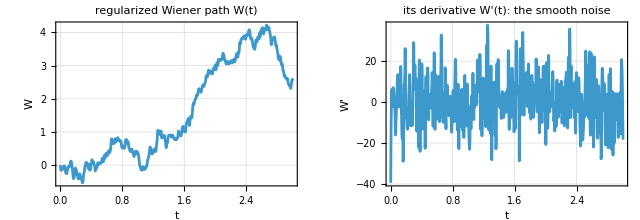

```mathematica
With[{Wf = wienerFun[tfB, dtGenOf[ratesB], 11]},
 GraphicsRow[{
   Plot[Wf[t], {t, 0, tfB}, Frame -> True, GridLines -> Automatic,
    PlotLabel -> "regularized Wiener path W(t)", FrameLabel -> {"t", "W"}],
   Plot[Wf'[t], {t, 0, tfB}, Frame -> True, GridLines -> Automatic,
    PlotLabel -> "its derivative W'(t): the smooth noise", FrameLabel -> {"t", "W'"}]},
  ImageSize -> 640]]
```

As one can see, W(t) is a continuous random walk and W'(t) is a jagged but genuine function, varying on the scale Δ t_gen. There are two time increments here, and they play different roles. The first, Δ t_gen, is the grid the Gaussian increments are drawn on: it sets the correlation time of the smoothed noise, and it is the dial that fixes which stochastic equation we actually solve, converging to the ideal white-noise SDE only as Δ t_gen→0. The second, the NDSolve step, carries no physics; it only has to resolve the forcing W'(t), smooth between noise knots, and we cap it below Δ t_gen, which forces several solver steps across each noise interval, keeps a step from straddling many derivative jumps, and supplements the adaptive error control. Which of the two actually moves the answer is a question we put to the machine below.

Assemble one trajectory. Build a smooth noise, form the random ODE OverDot[v⃗]=(a⃗)_Strat(v⃗)+(b⃗)_Strat(v⃗) W'(t) for the full four-vector, and hand it to NDSolve with its MaxStepSize capped below Δ t_gen:

```mathematica
ClearAll[oneTraj];
oneTraj[r_, init_, tf_, dtGen_, seed_, maxstep_, goal_ : Automatic] :=
  Module[{Wf, xx, yy, zz, QQ, t, rhs, eqs},
   Wf = wienerFun[tf, dtGen, seed];
   rhs = driftStrat[{xx[t], yy[t], zz[t], QQ[t]}, r] +
     diffStrat[{xx[t], yy[t], zz[t], QQ[t]}, r] Wf'[t];
   eqs = Join[MapThread[#1'[t] == #2 &, {{xx, yy, zz, QQ}, rhs}],
     {xx[0] == init[[1]], yy[0] == init[[2]], zz[0] == init[[3]], QQ[0] == init[[4]]}];
   NDSolveValue[eqs, {xx, yy, zz, QQ}, {t, 0, tf}, MaxStepSize -> maxstep,
    AccuracyGoal -> goal, PrecisionGoal -> goal]];
```

Show one trajectory two ways: the monitored component z(t) against the exact Lindblad mean, and the readout Q(t) it accumulates, both built from the single four-vector solution:

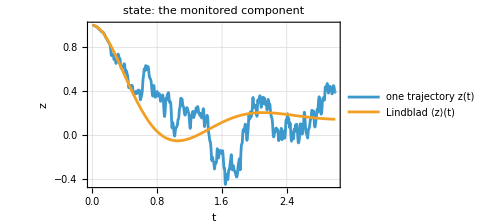
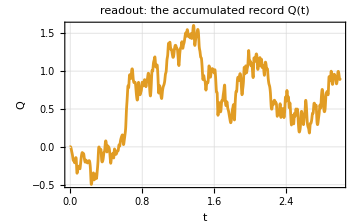

```mathematica
With[{traj = oneTraj[ratesB, initB, tfB, dtGenOf[ratesB], 7, dtGenOf[ratesB]/4],
   lb = lindbladBloch[ratesB, initB[[1 ;; 3]]]},
 Row[{
   Plot[{traj[[3]][t], lb[t][[3]]}, {t, 0, tfB},
    PlotLegends -> Placed[{"one trajectory z(t)", "Lindblad ⟨z⟩(t)"}, Below],
    Frame -> True, GridLines -> Automatic, FrameLabel -> {"t", "z"},
    PlotLabel -> "state: the monitored component", ImageSize -> Medium], "   ",
   Plot[traj[[4]][t], {t, 0, tfB}, PlotStyle -> ColorData[97, 2],
    Frame -> True, GridLines -> Automatic, FrameLabel -> {"t", "Q"},
    PlotLabel -> "readout: the accumulated record Q(t)", ImageSize -> Medium]}]]
```

As one can see, the state path fluctuates around the Lindblad mean, as a single record must, while the readout Q climbs steeply where z is near one and bends as z falls, its √Γ_CI z signal buried under noise. The two panels share one dW, and that is the physical content of a measurement record: the noise written into Q is the same noise that kicked z.

## The ensemble: matching the mean and the spread

A single path tells us little; the mean lives in the ensemble and the noise in how widely the paths spread. Rather than compare final values, we keep the whole trajectory from each route, average many of them, and watch the two ensemble means track the exact Lindblad curve across the entire interval. The two routes are the built-in StratonovichProcess integrator, which discretizes the target Stratonovich SDE, and the regularized NDSolve route, whose smooth ODE approaches that same SDE as Δ t_gen→0; the yardstick is a single Lindblad solution from DSolve.

Before any simulation, the central claim can be settled exactly, by the same built-in we are keeping. We never hand-compute the Itô-Stratonovich correction, but the conversion ItoProcess[StratonovichProcess[...]] applies it for us, rewriting our Stratonovich vector field in Itô form. If the explicit Stratonovich drift truly carries the correction, its Itô form must be the affine drift a⃗ we encoded as driftIto for the Lindblad reference, with the readout row untouched. Convert the full four-component field and subtract that target, under the physical assumption that the rates are nonnegative (needed only to fold √Γ_CI √Γ_BA into a single root):

```mathematica
Assuming[{Subscript[Γ, "CI"] >= 0, Subscript[Γ, "BA"] >= 0},
 FullSimplify[
  (ItoProcess[StratonovichProcess[{driftStrat[{x, y, z, q}, ratesSym],
        List /@ diffStrat[{x, y, z, q}, ratesSym], {x, y, z, q}},
       {{x, y, z, q}, {x0, y0, z0, q0}}, t]]["Drift"] /. {x[t] -> x, y[t] -> y, z[t] -> z, q[t] -> q})
   - Append[driftIto[{x, y, z}, ratesSym], Sqrt[Subscript[Γ, "CI"]] z]]]
```

{0,0,0,0}

The difference vanishes row by row: the Itô form of the Stratonovich SDE we hand NDSolve is exactly the affine drift on all three Bloch rows, and the readout row is unchanged, so the correction is carried in full and Q is the same in both calculi. This settles the central claim at no numerical cost and more decisively than any Monte-Carlo match; the ensemble below only confirms what the algebra already proves. One corollary in one line: switch the measurement off and the two calculi must coincide, because only the measurement noise separates them:

```mathematica
Simplify[(driftStrat[{x, y, z, q}, ratesSym] -
    Append[driftIto[{x, y, z}, ratesSym], Sqrt[ratesSym[[1]]] z]) /.
  {ratesSym[[1]] -> 0, ratesSym[[2]] -> 0}]
```

{0,0,0,0}

With Γ_CI=Γ_BA=0 the entire gap between the Stratonovich and Itô drifts closes: the correction is measurement backaction and nothing else.

Start the worker kernels:

```mathematica
LaunchKernels[];
```

Share the definitions the regularized trajectory needs, so ParallelTable can spread the paths across cores:

```mathematica
DistributeDefinitions[driftStrat, diffStrat, wienerFun, oneTraj];
```

Generate ntraj full trajectories from the built-in StratonovichProcess integrator, keeping every step of each path. Feed it the same Stratonovich drift and diffusion the NDSolve route uses, all four rows, and ask for the order-3/2 scalar-noise method rather than the default Euler-Maruyama, whose average carries a bias proportional to the step and so drifts off the exact curve at any finite step. The process variables are Wolfram's formal symbols, unbound by construction, so they are safe placeholders:

```mathematica
ClearAll[stratRun];
stratRun[r_, init_, tf_, dt_, ntraj_, seed_] :=
  Module[{t, v, proc, td},
   v = {x[t], y[t], z[t], q[t]};
   proc = StratonovichProcess[{driftStrat[v, r], List /@ diffStrat[v, r], v},
     {{x, y, z, q}, init}, t];
   td = BlockRandom[SeedRandom[seed];
     RandomFunction[proc, {0., tf, dt}, ntraj, Method -> "StochasticRungeKuttaScalarNoise"]];
   td["ValueList"]];
```

Generate the same count of regularized trajectories, each NDSolve solution read off on a shared time grid, keeping all four components so the record stays beside the state that produced it. Two arguments carry defaults so the one real relationship lives in one place: the integrator step is Δ t_gen/4, held a factor of four below the noise grid, and the read-off grid is the noise grid itself:

```mathematica
ClearAll[regRun];
regRun[r_, init_, tf_, dtGen_, ntraj_, baseSeed_, maxstep_ : Automatic, grid_ : Automatic] :=
  With[{ms = maxstep /. Automatic -> dtGen/4, g = grid /. Automatic -> noiseGrid[tf, dtGen]},
   ParallelTable[
    With[{tr = oneTraj[r, init, tf, dtGen, baseSeed + i, ms]},
     Transpose[#[g] & /@ tr]],
    {i, ntraj}]];
```

For the harder regimes and the step-size study below we will want only the final values, so reduce each generator to them. The native final Bloch vectors:

```mathematica
ClearAll[stratRef];
stratRef[r_, init_, tf_, dt_, ntraj_, seed_] := stratRun[r, init, tf, dt, ntraj, seed][[All, -1, 1 ;; 3]];
```

And the regularized final Bloch vectors, read off at t_f alone, the integrator step defaulting the same way:

```mathematica
ClearAll[ensemble];
ensemble[r_, init_, tf_, dtGen_, ntraj_, baseSeed_, maxstep_ : Automatic] :=
  regRun[r, init, tf, dtGen, ntraj, baseSeed, maxstep, {tf}][[All, -1, 1 ;; 3]];
```

Run both on the representative case, on the shared grid set by dtGenOf[ratesB]. First the native ensemble:

```mathematica
stratRunB = stratRun[ratesB, initB, tfB, dtGenOf[ratesB], nB, 2024];
```

Then the regularized ensemble on the same grid:

```mathematica
regRunB = regRun[ratesB, initB, tfB, dtGenOf[ratesB], nB, 9100];
```

Average each ensemble over its trajectories and compare the two mean paths of ⟨z⟩ against the single exact Lindblad trajectory:

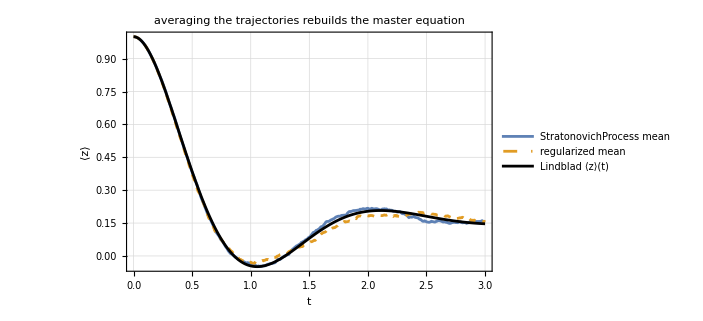

```mathematica
With[{g = noiseGrid[tfB, dtGenOf[ratesB]], lb = lindbladBloch[ratesB, initB[[1 ;; 3]]]},
 ListLinePlot[{
    Transpose[{g, Mean[stratRunB][[All, 3]]}],
    Transpose[{g, Mean[regRunB][[All, 3]]}],
    Transpose[{g, lb[#][[3]] & /@ g}]},
   PlotStyle -> {ColorData[97, 1], Directive[Dashed, ColorData[97, 2]], Directive[Thick, Black]},
   PlotLegends -> {"StratonovichProcess mean", "regularized mean", "Lindblad ⟨z⟩(t)"},
   Frame -> True, GridLines -> Automatic, FrameLabel -> {"t", "⟨z⟩"},
   PlotLabel -> "averaging the trajectories rebuilds the master equation", ImageSize -> 520]]
```

Note that both ensemble means, the built-in StratonovichProcess integrator and the regularized route, lie on the exact Lindblad curve across the whole interval, not only at the final time. Averaging over the trajectories rebuilds the deterministic master equation, which is the sense in which the smooth Lindblad flow was an average over jagged records all along.

Quantify "on the curve" rather than eyeball it: the largest gap between the regularized mean of z and the Lindblad value anywhere on the grid, in Monte-Carlo standard errors, skipping t=0 where all paths coincide and the standard error vanishes:

```mathematica
With[{g = Rest[noiseGrid[tfB, dtGenOf[ratesB]]], lb = lindbladBloch[ratesB, initB[[1 ;; 3]]],
  zc = regRunB[[All, 2 ;;, 3]]},
 Max[Abs[Mean[zc] - (lb[#][[3]] & /@ g)]/(StandardDeviation[zc]/Sqrt[nB])]]
```

2.81908

This is the worst standardized gap along the whole curve, the mean-to-Lindblad distance in units of the Monte-Carlo standard error; it stays within the scatter a maximum over hundreds of correlated read-offs produces by chance, so the mean sits on the master-equation curve everywhere, not merely at the end.

The mean sees only the drift, so it is a weak test. The measurement backaction lives in the standard deviation of the final Bloch vector, its spread across the ensemble, compared across the two routes:

```mathematica
TableForm[
 Transpose[{StandardDeviation[stratRunB[[All, -1, 1 ;; 3]]], StandardDeviation[regRunB[[All, -1, 1 ;; 3]]]}],
 TableHeadings -> {{"x", "y", "z"}, {"Stratonovich", "regularized"}}]
```

| Stratonovich | regularized
x | 0. | 0.
y | 0.211833 | 0.217951
z | 0.270725 | 0.27629

As one can see, the spreads agree component by component, so the regularized route reproduces the noise, not just the drift. The x row is flat zero: with the backaction quadrature off (Γ_BA=0) and no initial x-coherence, nothing sources x, and the substance sits in y and z. That flat zero is exact, not numerical: at Γ_BA=0 the x row of both the drift and the diffusion vanishes on the x=0 plane, so the plane is invariant for every remaining rate:

```mathematica
Simplify[{driftStrat[{0, y, z, q}, ratesSym][[1]], diffStrat[{0, y, z, q}, ratesSym][[1]]} /.
  ratesSym[[2]] -> 0]
```

{0,0}

"Agree" needs a scale, though: a spread estimated from finitely many samples is itself uncertain, with standard error √((m_4-s^4)/(4 s^2 n)), where m_4 is the sample's own fourth central moment (for near-Gaussian samples this reduces to the familiar spread over √(2n); taking it from the samples themselves costs nothing and assumes nothing about their shape), and the gap between two such estimates is uncertain by their errors in quadrature. In other words, a spread is itself a measurement with an error bar, and two spreads disagree only when their gap outruns that bar. Define that statistic once and read the two live components:

```mathematica
ClearAll[sdErr, spreadGap];
sdErr[x_] := With[{v = CentralMoment[x, 2]}, Sqrt[(CentralMoment[x, 4] - v^2)/(4 v Length[x])]];
spreadGap[x1_, x2_] := Abs[StandardDeviation[x1] - StandardDeviation[x2]]/
   Sqrt[sdErr[x1]^2 + sdErr[x2]^2];
TableForm[spreadGap[stratRunB[[All, -1, 2 ;; 3]], regRunB[[All, -1, 2 ;; 3]]],
 TableHeadings -> {{"y", "z"}}]
```

y | 0.800898
z | 0.58852

Both gaps sit at the size sampling error alone allows, so at this ensemble size the two routes' spreads are statistically indistinguishable.

The state should stay inside the unit ball, because the trajectory is a positivity-preserving unraveling of a Lindblad equation, and the admissibility condition tested above is exactly what enforces that. Here is the promised derivation. The radial component of the noise, (x,y,z)·b⃗=√Γ_CI z (1-x^2-y^2-z^2), vanishes on the unit sphere. Equivalently, the noise moves the state along the sphere, never through it, so whether a path can cross is decided by the Itô drift of r^2=x^2+y^2+z^2 there, which is 2 (x,y,z)·a⃗+b⃗·b⃗ on the three state rows, the readout row playing no part in the radius, evaluated at r=1 and with the closed form

((d ⟨r^2⟩)/dt|)_(r=1)=(1-z^2) (Γ_CI+Γ_BA-2(Γ_d+γ_ϕ))-γ_1(1-z)^2.

Verify that closed form, substituting a point on the sphere and subtracting the claim:

```mathematica
With[{b3 = diffStrat[{x, y, z, q}, ratesSym][[1 ;; 3]]},
 Simplify[((2 {x, y, z} . driftIto[{x, y, z}, ratesSym] + b3 . b3) /.
     {x -> Sqrt[1 - z^2] Cos[ϕ], y -> Sqrt[1 - z^2] Sin[ϕ]}) -
   ((1 - z^2) (ratesSym[[1]] + ratesSym[[2]] - 2 (ratesSym[[3]] + ratesSym[[4]])) -
     ratesSym[[5]] (1 - z)^2)]]
```

0

The subtraction cancels identically, so the closed form is exact. Read it: the relaxation term -γ_1(1-z)^2 always pulls inward but dies quadratically at the ground pole, while the measurement bracket scales as (1-z^2) and survives there linearly, so the drift points inward for every z precisely when Γ_CI+Γ_BA≤2(Γ_d+γ_ϕ), the admissibility condition. Every rate set that drives an ensemble in this document passes that test in the cell defining it; of the three single-path sets below, one is a deliberate violation and the other two sit exactly on the admissibility boundary, each named as such where it appears. So the largest Bloch radius any regularized path reached, over the stored grid, should sit at one to within the small overshoot of an unprojected scheme:

```mathematica
Max[Map[Norm, regRunB[[All, All, 1 ;; 3]], {2}]]
```

1.

The radius sits at one to within a hair, with no projection step. Read this as a spot-check of positivity, not a proof of it: it samples one ensemble on a fixed grid from a state that began on the surface. Violate the admissibility condition, which for a detector means η>1+γ_ϕ/Γ_d, more information extracted than the dephasing paid for, and the equation stops being a valid unraveling: the trajectory can leave the ball, and its coordinates no longer describe a density matrix. That failure is one cell away. Fix rates that fail the check, twice the information the dephasing supplies, start on the sphere away from the pole where the closed form above makes the flux point outward, and read the largest radius one path reaches:

```mathematica
With[{ratesBad = {2., 0., 0.5, 0., 1., 0.}},
 With[{tr = oneTraj[ratesBad, {0.8, 0., 0.6, 0.}, 1., dtGenOf[ratesBad], 5, dtGenOf[ratesBad]/4]},
  Max[Norm /@ Transpose[#[Subdivide[0., 1., 200]] & /@ tr[[1 ;; 3]]]]]]
```

1.02473

The radius runs past one: on this part of the sphere the drift itself points outward, so the exit is deterministic, not a rare fluctuation. The equation still integrates; what fails is its meaning, since no density matrix has a Bloch vector outside the ball.

The boundary is just as sharp from the inside. Saturate the condition with no relaxation and no intrinsic dephasing, γ_1=γ_ϕ=0 with both quadratures on and the drive on too, Γ_CI+Γ_BA=2 Γ_d exactly, and the closed form above vanishes identically: the sphere itself is invariant, so a pure state stays pure along every single trajectory, not merely on average. Start a path on the sphere and read how far it ever leaves:

```mathematica
With[{rPure = {0.352, 0.4, 0.376, 0., 0., 3.}},
 With[{tr = oneTraj[rPure, {0.6, 0., 0.8, 0.}, 3., dtGenOf[rPure], 5, dtGenOf[rPure]/4],
   s = Subdivide[0., 3., 400]},
  Max[Abs[Norm /@ Transpose[#[s] & /@ tr[[1 ;; 3]]] - 1]]]]
```

5.7942×10^-6

The radius sticks to the sphere at solver error, the sharpest test of the diffusion's scale in the document: a noise term wrong by any factor would walk the path off the sphere at once. On the boundary, positivity is not an inequality respected but an equality enforced.

## The readout: the average signal and the shared noise

We carried the readout Q beside the state through every run but have only looked at the state. Turn to the record itself. Taking the mean of dQ=√Γ_CI z dt+dW and using ⟨dW⟩=0, the average record is the integrated signal,

⟨Q(t)⟩=√Γ_CI∫_0^t ⟨z(s)⟩ ds,

a closed prediction we already hold, since ⟨z⟩ is the Lindblad mean. And the records are already in hand: every stored trajectory carries Q as its fourth component, so slice the record ensemble out of the same run whose state we just averaged:

```mathematica
recQB = regRunB[[All, All, 4]];
```

The prediction is itself a closed form, not a quadrature: append u'=√Γ_CI ⟨z⟩ to the affine system and let DSolve integrate it exactly:

```mathematica
ClearAll[qpredB];
qpredB = Module[{sol, xf, yf, zf, uf, t},
   sol = DSolve[Join[MapThread[#1'[t] == #2 &, {{xf, yf, zf}, driftIto[{xf[t], yf[t], zf[t]}, ratesB]}],
       {uf'[t] == Sqrt[ratesB[[1]]] zf[t], xf[0] == initB[[1]], yf[0] == initB[[2]],
        zf[0] == initB[[3]], uf[0] == 0}], {xf, yf, zf, uf}, t] // First;
   Function[tt, Re[uf[tt] /. sol]]];
```

Overlay the ensemble-averaged record on that prediction:

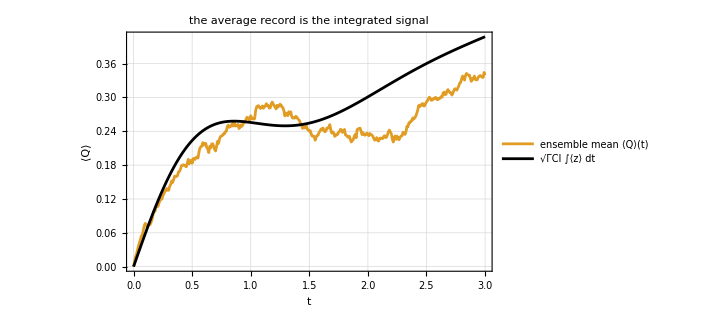

```mathematica
With[{g = noiseGrid[tfB, dtGenOf[ratesB]]},
 ListLinePlot[{Transpose[{g, Mean[recQB]}], Transpose[{g, qpredB /@ g}]},
  PlotStyle -> {ColorData[97, 2], Directive[Thick, Black]},
  PlotLegends -> {"ensemble mean ⟨Q⟩(t)", "√ΓCI ∫⟨z⟩ dt"},
  Frame -> True, GridLines -> Automatic, FrameLabel -> {"t", "⟨Q⟩"},
  PlotLabel -> "the average record is the integrated signal", ImageSize -> 520]]
```

As expected, the mean record climbs along the integrated ⟨z⟩, the two curves tracking with a residual wander that is the ensemble-averaged noise, of order √(t/n_traj) and not yet fully cancelled at this sample size. The signal is what survives averaging; the noise is what does not.

Turn that visual match into a number: the largest gap between the mean record and its prediction anywhere on the grid, in Monte-Carlo standard errors, again skipping the start where the record is pinned at zero:

```mathematica
With[{g = Rest[noiseGrid[tfB, dtGenOf[ratesB]]], qc = recQB[[All, 2 ;;]]},
 Max[Abs[Mean[qc] - (qpredB /@ g)]/(StandardDeviation[qc]/Sqrt[nB])]]
```

1.66269

Again the worst standardized gap along the window: it stays within what sampling noise alone produces, so the mean record is the integrated signal everywhere on the grid, which is all the average can claim at finite n_traj.

The record's spread deserves the same two-route treatment as the state's, and the native ensemble has been carrying the fourth row all along; read its final-Q spread against the regularized ensemble's, in the same units as before:

```mathematica
spreadGap[stratRunB[[All, -1, 4]], recQB[[All, -1]]]
```

0.910011

The record's final spread agrees between the routes at the sampling scale too: beyond its mean and its pathwise identity, the record's spread now has an independent reference, so the fourth row is held to the same standard as the state.

The average removed the noise, but a single record still carries it, and carries a specific one. Since dQ-√Γ_CI z dt=dW exactly, subtracting the integrated signal from one record must return the very Wiener path that drove the state. Build one trajectory, strip its signal, and overlay the remainder on its driving path W(t):

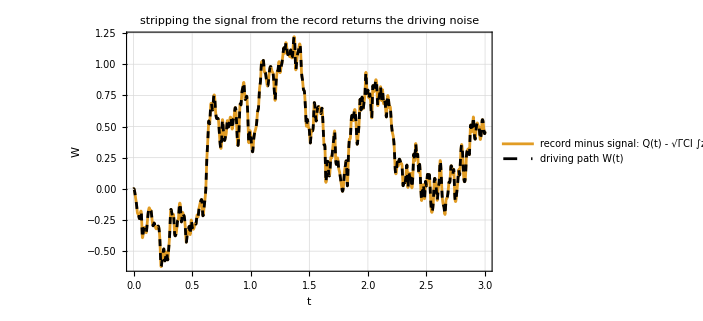

```mathematica
With[{r = ratesB, dt = dtGenOf[ratesB], seed = 7},
 With[{Wf = wienerFun[tfB, dt, seed], traj = oneTraj[r, initB, tfB, dt, seed, dt/4]},
  Module[{u, t, zint},
   zint = NDSolveValue[{u'[t] == traj[[3]][t], u[0] == 0.}, u, {t, 0, tfB}];
   Plot[{traj[[4]][t] - Sqrt[r[[1]]] zint[t], Wf[t]}, {t, 0, tfB},
    PlotStyle -> {Directive[Thick, ColorData[97, 2]], Directive[Dashed, Black]},
    PlotLegends -> Placed[{"record minus signal: Q(t) - √ΓCI ∫z dt", "driving path W(t)"}, Below],
    Frame -> True, GridLines -> Automatic, FrameLabel -> {"t", "W"},
    PlotLabel -> "stripping the signal from the record returns the driving noise", ImageSize -> 520]]]]
```

Notice that the stripped record lands on the driving path to the width of the line. This is the physical content of a measurement made literal: the fluctuations in the record are not merely correlated with the noise that kicked the state, they are that noise. The observer reads √Γ_CI∫z as signal; the remainder is the single innovation dW the detector wrote into the record and the backaction at once.

Rather than trust the line width, put a number on it, the largest gap between the stripped record and the driving path across the window; define the residual once, its solver goals adjustable, and read it at the default tolerance:

```mathematica
ClearAll[recordResidual];
recordResidual[goal_] := With[{r = ratesB, dt = dtGenOf[ratesB], seed = 7},
   With[{Wf = wienerFun[tfB, dt, seed], traj = oneTraj[r, initB, tfB, dt, seed, dt/4, goal]},
    Module[{u, t, zint},
     zint = NDSolveValue[{u'[t] == traj[[3]][t], u[0] == 0.}, u, {t, 0, tfB},
       AccuracyGoal -> goal, PrecisionGoal -> goal];
     With[{s = Subdivide[0., tfB, 1000]},
      Max[Abs[traj[[4]][s] - Sqrt[r[[1]]] zint[s] - Wf[s]]]]]]];
recordResidual[Automatic]
```

1.28591×10^-6

The residual is pure solver error, and note what this cell is: the same ODE defines Q'=√Γ_CI z+W', so stripping the signal is a self-consistency check that the integrator preserves the defining record identity, not an independent validation of the route. If that reading is right, the residual must fall when the solver is asked for more digits. Rerun the same trajectory with AccuracyGoal and PrecisionGoal tightened:

```mathematica
recordResidual[10]
```

3.7378×10^-8

The residual falls with the tolerance, confirming it is integration error and nothing else: the record minus its signal is the driving noise as an identity, at whatever precision the solver is asked to keep.

One regime makes the tie between the state and its record total. Switch off relaxation and drive, γ_1=Ω_x=0, and leave everything else alone: backaction, dephasing, any efficiency. Those only kick the phase, never the population, so dividing the Stratonovich z row by 1-z^2 turns the ordinary chain rule loose, d arctanh z=Γ_CI z dt+√Γ_CI dW=√Γ_CI dQ, and the monitored component becomes a closed function of its own accumulated record, z(t)=tanh (arctanh z_0+√Γ_CI Q(t)), exactly and pathwise. In other words, with nothing but measurement acting, the record is a complete log of the state. First check the differential identity on the whole symbolic flow, the formal w standing in for the noise:

```mathematica
With[{rFree = ReplacePart[ratesSym, {5 -> 0, 6 -> 0}]},
 Simplify[(driftStrat[{x, y, z, q}, rFree][[3]] + diffStrat[{x, y, z, q}, rFree][[3]] w)/(1 - z^2) -
   Sqrt[rFree[[1]]] (driftStrat[{x, y, z, q}, rFree][[4]] + diffStrat[{x, y, z, q}, rFree][[4]] w)]]
```

0

The identity holds with Γ_BA,Γ_d,γ_ϕ fully symbolic: reading the state off the record is filtering, and the trajectory does it at any efficiency; only relaxation or a drive can decouple z from its own record. Now read the largest violation along one regularized path, at a bare-measurement rate set that sits exactly on the admissibility boundary, Γ_CI=2 Γ_d with γ_ϕ=0; make the residual's solver goals adjustable, like the record residual above:

```mathematica
ClearAll[rG, tanhResidual];
rG = {0.352, 0., 0.176, 0., 0., 0.};
tanhResidual[goal_] := With[{z0 = 0.6},
   With[{tr = oneTraj[rG, {0., 0., z0, 0.}, tfB, dtGenOf[rG], 11, dtGenOf[rG]/4, goal],
     s = Subdivide[0., tfB, 1000]},
    Max[Abs[tr[[3]][s] - Tanh[ArcTanh[z0] + Sqrt[rG[[1]]] tr[[4]][s]]]]]];
tanhResidual[Automatic]
```

1.17008×10^-6

Tighten the goals and the violation must follow the solver, not the noise grid:

```mathematica
tanhResidual[10]
```

4.51974×10^-8

It falls with the tolerance: under the Stratonovich reading the chain rule is exact at any Δ t_gen, so nothing about this identity waits for the white-noise limit. Where the general case shares one noise between state and record, this regime goes further: the state is the record, read through a tanh.

## The two time steps: which one sets the answer

The route carries two time increments, and the section title is a real question: which of them moves the answer? Put the integrator step to the test first. Hold the noise grid fixed and read the final-z mean and spread with the NDSolve step held far below Δ t_gen, then again with it pushed well above; the first row reads the run already stored, the second re-integrates the same noise with the cap relaxed:

```mathematica
TableForm[
 Map[{Mean[#][[3]], StandardDeviation[#][[3]]} &,
  {regRunB[[All, -1, 1 ;; 3]],
   ensemble[ratesB, initB, tfB, dtGenOf[ratesB], nB, 9100, 10 dtGenOf[ratesB]]}],
 TableHeadings -> {{"step Δt_gen/4",
    "step 10 Δt_gen"}, {"mean z", "spread z"}}]
```

| mean z | spread z
step Δt_gen/4 | 0.15489 | 0.27629
step 10 Δt_gen | 0.15489 | 0.27629

As one can see, with the same noise realizations under both, the two rows coincide to solver precision: for this parameter set and NDSolve's default tolerances, its adaptive error control refines the step wherever W'(t) varies, so relaxing MaxStepSize from a quarter of Δ t_gen to ten times it leaves the observables unmoved. We still cap it below Δ t_gen as a cheap guarantee, not because this run needs it, and it is not the binding dial.

The binding dial is Δ t_gen, and the native StratonovichProcess ensemble is the reference the shrinking grid should approach. Read its final-z mean:

```mathematica
Mean[stratRunB[[All, -1, 3]]]
```

0.155673

and its final-z spread, the number the regularized route must reproduce as the grid tightens:

```mathematica
StandardDeviation[stratRunB[[All, -1, 3]]]
```

0.270725

A reference earns its role only if it is converged itself, so put the same question to the native integrator. The first row is the working step, the very ensemble serving as reference; below it the step is halved and halved again, the spreads stored for the comparison that follows:

```mathematica
natZB = Prepend[Table[stratRef[ratesB, initB, tfB, dtGenOf[ratesB]/f, nB, 2024][[All, 3]],
    {f, {2, 4}}], stratRunB[[All, -1, 3]]];
TableForm[Transpose[{dtGenOf[ratesB]/{1, 2, 4}, StandardDeviation /@ natZB}],
 TableHeadings -> {None, {"dt", "spread z"}}]
```

dt | spread z
0.00833333 | 0.270725
0.00416667 | 0.274802
0.00208333 | 0.259568

Read the two refined rows as distances from the working-step row, in units of the estimates' sampling errors in quadrature:

```mathematica
TableForm[spreadGap[#, First[natZB]] & /@ Rest[natZB], TableHeadings -> {{"dt/2", "dt/4"}}]
```

dt/2 | 0.432431
dt/4 | 1.23381

Both refined steps sit at the sampling scale of the working step, with no systematic trend, so at the working step the native ensemble is a converged yardstick for the comparisons above and the sweep below.

Now sweep Δ t_gen from coarse to fine, the integrator step held below it, and tabulate the regularized mean and spread of the final z against the grid step:

```mathematica
nSweep = 300;
sweepZB = Table[ensemble[ratesB, initB, tfB, tfB/k, nSweep, 6000][[All, 3]], {k, {6, 12, 25, 100, 400}}];
TableForm[Transpose[{N[tfB/{6, 12, 25, 100, 400}], Mean /@ sweepZB, StandardDeviation /@ sweepZB}],
 TableHeadings -> {None, {"Δt_gen", "mean z", "spread z"}}]
```

Δt_gen | mean z | spread z
0.5 | 0.133827 | 0.312211
0.25 | 0.134609 | 0.264616
0.12 | 0.160865 | 0.255801
0.03 | 0.143051 | 0.258983
0.0075 | 0.116075 | 0.26269

As expected, the estimated means stay compatible with the Lindblad value within the Monte-Carlo scatter while the spread descends from an inflated coarse value and flattens toward the native reference as Δ t_gen shrinks. In the white-noise limit the affine drift fixes the mean exactly; at finite Δ t_gen any regularization bias in the mean sits below the Monte-Carlo scatter here, while the bias in the spread is large enough to watch converge out. Put the mean column in its own units, each row's distance from the exact Lindblad value in that row's standard error:

```mathematica
With[{lbz = lindbladBloch[ratesB, initB[[1 ;; 3]]][tfB][[3]]},
 TableForm[Abs[Mean[#] - lbz]/(StandardDeviation[#]/Sqrt[nSweep]) & /@ sweepZB,
  TableHeadings -> {N[tfB/{6, 12, 25, 100, 400}]}]]
```

0.5 | 0.712249
0.25 | 0.789189
0.12 | 0.961412
0.03 | 0.241777
0.0075 | 2.01697

All five distances sit where sampling noise puts the largest of a handful of draws, with no growth as the grid coarsens, so the mean carries no resolvable regularization bias at any of these grids: the affine drift doing exactly what the algebra said it must. So of the two increments it is Δ t_gen that sets the answer, and at this sampling accuracy the spread is where we can see it move.

## Phase backaction: the x channel comes alive

So far the backaction quadrature has been off (Γ_BA=0), which decoupled x and left it trivial. Turn it on and the x channel comes alive, but watch where: the affine Itô drift still decouples x's mean, so ⟨x⟩ decays on its own, while the diffusion's √Γ_BA y term now feeds x's fluctuations from y. So the mean is the weak test of the coupling and the spread is the real one. Fix a case with both quadratures on, from a tilted start. This set satisfies the admissibility condition with equality, Γ_CI+Γ_BA=2(Γ_d+γ_ϕ) with γ_ϕ=0: a quantum-limited detector (η=1) and nothing else dephasing, so run the check as an equality:

```mathematica
ratesX = {0.4, 0.4, 0.4, 0., 1., 2.}; initX = {0.3, 0., 0.6, 0.}; tfX = 2.; nX = 600;
ratesX[[1]] + ratesX[[2]] == 2 (ratesX[[3]] + ratesX[[4]])
```

True

Read its efficiency too:

```mathematica
efficiency[ratesX]
```

1.

Run the native reference:

```mathematica
stratX = stratRef[ratesX, initX, tfX, dtGenOf[ratesX], nX, 4040];
```

Run the regularized ensemble:

```mathematica
regX = ensemble[ratesX, initX, tfX, dtGenOf[ratesX], nX, 7100];
```

Compare the mean of the final Bloch vector across the three routes:

```mathematica
TableForm[
 Transpose[{lindbladBloch[ratesX, initX[[1 ;; 3]]][tfX], Mean[stratX], Mean[regX]}],
 TableHeadings -> {{"x", "y", "z"}, {"Lindblad", "Stratonovich", "regularized"}}]
```

| Lindblad | Stratonovich | regularized
x | 0.0495897 | 0.0530804 | 0.0439081
y | -0.40219 | -0.380895 | -0.394597
z | 0.0979237 | 0.121102 | 0.0935365

Note that the x row is now genuinely nonzero and the three routes agree on it, its mean decaying under the drift that decouples it. Now the spread, where the backaction actually lives across the two routes:

```mathematica
TableForm[
 Transpose[{StandardDeviation[stratX], StandardDeviation[regX]}],
 TableHeadings -> {{"x", "y", "z"}, {"Stratonovich", "regularized"}}]
```

| Stratonovich | regularized
x | 0.234983 | 0.228004
y | 0.275807 | 0.274058
z | 0.336436 | 0.33498

As expected, the x spread is now substantial, fed by the backaction noise the y channel injects, and the regularized route matches it. Same scale test as before, now with all three components alive:

```mathematica
TableForm[spreadGap[stratX, regX], TableHeadings -> {{"x", "y", "z"}}]
```

x | 1.04478
y | 0.16396
z | 0.137283

All three gaps sit at the sampling scale, so the coupled channel's noise is reproduced quantitatively, not just visibly. This is the full-Bloch-vector check the representative case could not give: with the coupling on, every component carries a nonzero spread, and the regularized Stratonovich route reproduces all three.

## A strong readout: the same route where the drift is large

The gap between the Itô and Stratonovich drifts scales with the measurement rate, so a strong informative readout is the stringent test of feeding NDSolve the Stratonovich form. Fix a strong readout from a tilted start, again a four-vector with the readout zeroed; the rates are again quantum-limited (η=1), with the intrinsic dephasing supplying the slack in the admissibility check:

```mathematica
ratesS = {8., 0., 4., 1., 1., 3.}; initS = {0.6, 0., 0.6, 0.}; tfS = 1.5; nS = 600;
ratesS[[1]] + ratesS[[2]] <= 2 (ratesS[[3]] + ratesS[[4]])
```

True

Read its efficiency:

```mathematica
efficiency[ratesS]
```

1.

Run the native reference for the strong case:

```mathematica
stratS = stratRef[ratesS, initS, tfS, dtGenOf[ratesS], nS, 3030];
```

Run the regularized ensemble for the strong case:

```mathematica
regS = ensemble[ratesS, initS, tfS, dtGenOf[ratesS], nS, 5300];
```

Compare the mean of the final Bloch vector across the three routes:

```mathematica
TableForm[
 Transpose[{lindbladBloch[ratesS, initS[[1 ;; 3]]][tfS], Mean[stratS], Mean[regS]}],
 TableHeadings -> {{"x", "y", "z"}, {"Lindblad", "Stratonovich", "regularized"}}]
```

| Lindblad | Stratonovich | regularized
x | 0.000156755 | 0.00014778 | 0.000115805
y | -0.209168 | -0.214917 | -0.212706
z | 0.378355 | 0.390635 | 0.404132

As one can see, the regularized mean still tracks the exact value in every row where the correction is large; the x row has decayed from its initial tilt toward zero, since with Γ_BA=0 nothing rotates it back, and all three routes agree on the small residual. Compare the spread across the two routes:

```mathematica
TableForm[
 Transpose[{StandardDeviation[stratS], StandardDeviation[regS]}],
 TableHeadings -> {{"x", "y", "z"}, {"Stratonovich", "regularized"}}]
```

| Stratonovich | regularized
x | 0.000661504 | 0.000502005
y | 0.342519 | 0.333832
z | 0.699005 | 0.707963

As expected, the y and z spreads agree closely where the Stratonovich correction is largest; the x spread differs relatively but is negligible in absolute size in both routes, since with Γ_BA=0 nothing sources it. Put the sampling scale on the two live components again:

```mathematica
TableForm[spreadGap[stratS[[All, 2 ;; 3]], regS[[All, 2 ;; 3]]], TableHeadings -> {{"y", "z"}}]
```

y | 0.788843
z | 0.430146

Both gaps sit at the sampling scale even at strong coupling. See the final-z marginal agree, the regularized histogram against the native Stratonovich reference:

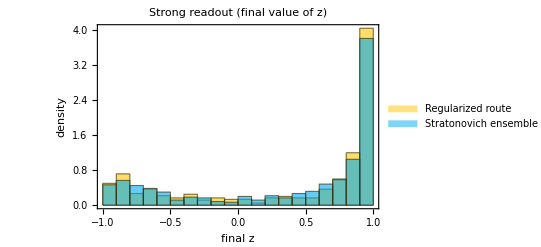

```mathematica
Histogram[{regS[[All, 3]], stratS[[All, 3]]}, 24, "PDF",
  Frame -> True, FrameLabel -> {"final z", "density"},
  PlotLabel -> "Strong readout (final value of z)", 
 PlotLegends -> {"Regularized route", "Stratonovich ensemble"}]
```

This confirms that the regularized histogram sits on top of the native Stratonovich reference: the route reproduces the final-z marginal, not merely its mean, even where the drift correction is strong.

The refinement sweep above checked forty knots per fastest rate only on the representative case; the strong readout, where the drift correction is largest, deserves its own. Tighten the noise grid toward the working value, storing the spreads for the comparison that follows:

```mathematica
sweepZS = Table[ensemble[ratesS, initS, tfS, tfS/k, nSweep, 6600][[All, 3]], {k, {120, 240, 480}}];
TableForm[Transpose[{N[tfS/{120, 240, 480}], StandardDeviation /@ sweepZS}],
 TableHeadings -> {None, {"Δt_gen", "spread z"}}]
```

Δt_gen | spread z
0.0125 | 0.716667
0.00625 | 0.748555
0.003125 | 0.69531

Now read each row as a distance from the native strong-case spread, in units of the two estimates' sampling errors in quadrature:

```mathematica
TableForm[spreadGap[#, stratS[[All, 3]]] & /@ sweepZS, TableHeadings -> {N[tfS/{120, 240, 480}]}]
```

0.0125 | 0.690612
0.00625 | 2.12706
0.003125 | 0.137119

A resolvable regularization bias would grow steadily as the grid coarsens; these distances show no such growth, so what the sweep measures is its own sampling noise: forty knots per fastest rate carries margin where the correction is strongest, not only where it is mild.

## What is now true

The trajectory of a continuously monitored qubit is one four-component stochastic differential equation: the three Bloch numbers and the readout the detector accumulates, all driven by a single noise. Written in Stratonovich form, its drift already carries the term that separates the two stochastic calculi, and the built-in Stratonovich-to-Itô conversion certifies that exactly, so a smooth-noise integrator needs nothing added: replace the white noise by a cubic-interpolated Wiener path, hand NDSolve the Stratonovich drift and diffusion as they stand, and the solution approaches the target Itô process as Δ t_gen→0.

The numerical evidence is finite-resolution agreement against two references, each held to its own standard: because the Itô drift is affine, the ensemble mean must be, and is, the Lindblad master equation, component by component at the final time and along the whole window for the monitored component; and the ensemble spread lands on the native StratonovichProcess ensemble in both the representative and the strong-readout regime, a reference itself checked stable under step refinement in the representative case and, carried with all four rows, one that fixes the record's final spread as well. Once both solvers are converged, Δ t_gen controls the remaining regularization bias, since it fixes which stochastic equation is actually being solved, while n_traj controls the statistical uncertainty of everything read from the ensemble; the integrator's step cap is absorbed by its own error control at the representative rates, while the record identity's residual, the one tolerance-sensitive quantity, is integration error and shrinks on demand.

Integrating the readout beside the state costs one more equation and buys the physics of a measurement record: averaged over the ensemble, the record is the integrated signal √Γ_CI∫⟨z⟩; stripped of that signal, a single record returns the very Wiener path that kicked the state, because the record and the backaction are one draw of the same noise; and in the bare-measurement regime the tie is total, the state a closed function of its own record through a tanh. And once the backaction quadrature is on, the x channel it feeds carries its own spread, which the route reproduces along with the rest, so the full Bloch vector is matched, not just the monitored component. All of it holds inside the admissibility condition Γ_CI+Γ_BA≤2(Γ_d+γ_ϕ) that keeps the unraveling a density matrix; outside it, the trajectory can leave the Bloch ball and stops describing a quantum state. What the record buys is the natural continuation: filtering the same four-component equation into a running estimate of the state, feeding that estimate back, and smoothing it after the fact.